```mathematica
Datos
```

```mathematica
Ni=50;
β=10^6;       
Ci=4.88;
Di=0.43;
ηLos=10^(0.1/10);
ηNLos=10^(21/10);
VC=3 10^8;
fc=2.5 10^9;
No=2.0019 10^-12;
Ki=1;
B=50 10^6;
Lxti=0;
Lxts=500;
Lyti=0;
Lyts=500;
Lzti=0;
Lzts=1;
Lxs={500,1000};
Lys={500,500};
Lxi={0,500};
Lyi={0,0};
Lzi={0,0};
Lzs={1,1};
μx=250;
μy=250;
μz=0.5;
σx=100;
σy=100;
σz=0.2;
α =2;
h=10;
```

```mathematica
Li and Joint
```

```mathematica
jointPDF3D[Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,x_,y_,z_,μx_,μy_,μz_,σx_,σy_,σz_]:=PDF[ProductDistribution[TruncatedDistribution[{Lxti,Lxts},NormalDistribution[μx,σx]],TruncatedDistribution[{Lyti,Lyts},NormalDistribution[μy,σy]],TruncatedDistribution[{Lzti,Lzts},NormalDistribution[μz,σz]]],{x,y,z}];
di[x_,xi_,y_,yi_,z_,hi_]:=Sqrt[(xi-x)^2+(yi-y)^2+(hi-z)^2];
βeta[x_,xi_,y_,yi_,z_,hi_]:=180/π ArcSin[(hi*Sqrt[(xi-x)^2+(yi-y)^2])/(di[x,xi,y,yi,z,hi] Sqrt[(xi-x)^2+(yi-y)^2+z^2])] ;
Plos[x_,xi_,y_,yi_,hi_,z_,Ci_,Di_]:=1/(1+Ci ⅇ^(-Di ( βeta[x,xi,y,yi,z,hi]-Ci))) ;

Li1[x_,xi_,y_,yi_,hi_,z_,Ci_,Di_,ηLos_,ηNLos_,fc_,VC_]:=Plos[x,xi,y,yi,hi,z,Ci,Di] *((4 Pi fc)/VC)^2 *di[x,xi,y,yi,z,hi]^α *ηLos +( ηNLos *(1- Plos[x,xi,y,yi,hi,z,Ci,Di])*di[x,xi,y,yi,z,hi]^α *((4 Pi fc)/VC)^2) ;

Mi[Ni_,Lxs_,Lys_,Lxi_,Lyi_,Lzs_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_, σy_,σz_ ]:= Ni* Abs[NIntegrate[jointPDF3D[Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,x,y,z,μx,μy,μz,σx,σy,σz],{x,Lxi,Lxs},{y,Lyi,Lys},{z,Lzi,Lzs}]];
```

```mathematica
Función Objetivo
```

```mathematica
ptG3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_ ,Ni_,x_,y_,z_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=(2^((β Mi[Ni,Lxs,Lys,Lxi,Lyi,Lzs,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx, σy,σz])/B)-1)*No* Li1[x,xi,y,yi,z,hi,Ci,Di,ηLos,ηNLos,fc,VC]*jointPDF3D[Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,x,y,z,μx,μy,μz,σx,σy,σz];

ptGNint3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=NIntegrate[ptG3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B, Ni,x,y,z,xi,yi,hi,No,ηLos,ηNLos,fc,VC],{x,Lxi,Lxs},{y,Lyi,Lys},{z,Lzi,Lzs}];
ptTotalKiUAVs3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=Sum[ptGNint3D[Ci,Di,Lxs[[i]],Lys[[i]],Lzs[[i]],Lxi[[i]],Lyi[[i]],Lzi[[i]],Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,xi[[All,i]],yi[[All,i]],hi,No,ηLos,ηNLos,fc,VC],{i,1,Ki}];
```

```mathematica
Llama la función
```

```mathematica
Objetivo1[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=Module[{},
xMod=ptTotalKiUAVs3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,xi,yi,hi,No,ηLos,ηNLos,fc,VC];
Return[xMod];
]
```

```mathematica
PSO-E-3D
```

```mathematica
PSOE3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_ ,Ni_,h_,No_,ηLos_,ηNLos_,fc_,VC_,Ki_]:=Module[{},
iteration = 3;
popSize= 2000;
(*Parametrizaion of PSO*)
tao=1;
tao1=0.2;
inercia1=0.5;
memorial1=2;
cooperacion1=3;
perturbacion1=0.1;
(*Límites de las variables*)
Dmin={200,200,10};
Dmax={300,300,200};
(*Dmin=ConstantArray[0,3*Ki];
Dmax=ConstantArray[200,3*Ki];*)
(*Dmin= {0,0,0} ;
Dmax ={200,200,200} ;*)
D1=Length [Dmin];
xx=ConstantArray[0, {popSize,D1}];
v=ConstantArray[0, {popSize, D1}]; 
fitness=ConstantArray[0,popSize];
(*Posicion inicial de las particulas*)
For[jj=1, jj<=D1, jj++,
xx[[All,jj]]=(Dmax[[jj]]-Dmin[[jj]])RandomReal[{0,1}, popSize]+Dmin[[jj]]
];
fitness=Objetivo1[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,xx[[All,1;;Ki]],xx[[All,Ki+1;;2*Ki]],h,No,ηLos,ηNLos,fc,VC];
{fgbest,indgbest}=Take[Flatten[MinimalBy[Transpose[{fitness,Range[popSize]}],First]],2];
xgbest=xx[[indgbest]];
fpbest=fitness;
xpbest=xx;
OF=ConstantArray[0, iteration];
For[count1=1, count1≤iteration, count1++,
OF[[count1]]=fgbest;
inercia = inercia1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
inercia=Clip[inercia,{0,1}];
memoria=memorial1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
memoria=Clip[memoria,{0,1}];
cooperacion=cooperacion1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
cooperacion=Clip[cooperacion,{0,1}];
xgbest=ConstantArray[xgbest,Length[xx]];
v=inercia*v+memoria*(xpbest-xx)+cooperacion*(xgbest-xx);
xx=xx+v;
xgbest=xgbest[[1]];
For[jj=1, jj<=D1, jj++,
xx[[All,jj]]=ReplacePart[xx[[All,jj]],Position[xx[[All,jj]],y_/;y<Dmin[[jj]]]->Dmin[[jj]]];
xx[[All,jj]]=ReplacePart[xx[[All,jj]],Position[xx[[All,jj]],y_/;y>Dmax[[jj]]]->Dmax[[jj]]];
];
fitness=Objetivo1[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,xx[[All,1;;Ki]],xx[[All,Ki+1;;2*Ki]],h,No,ηLos,ηNLos,fc,VC];
positions=Flatten[Position[Thread[fitness<fpbest],True]];
xpbest[[positions]]=xx[[positions]];
    fpbest[[positions]]=fitness[[positions]];
{fgbest,indgbest}=Take[Flatten[MinimalBy[Transpose[{fitness,Range[popSize]}],First]],2];
xgbest=Flatten[xx[[indgbest]]];
perturbacion=perturbacion1+tao1*Flatten[RandomReal[NormalDistribution[0,1],{1,Length[xgbest]}]];
perturbacion=Clip[perturbacion,{0,1}];
aux=xgbest+perturbacion;
aux={aux};
c1=Objetivo1[aux];
c2=c1[[1]];
If[fgbest>c2,
xgbest=aux;
xgbest=xgbest[[1]];
fgbest=Objetivo1[aux];
fgbest=fgbest[[1]];
];
];
Return[fgbest];
]
```

```mathematica
PSOE3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,h,No,ηLos,ηNLos,fc,VC,Ki]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

```mathematica
Fig3D2=ParallelTable[{h,PSOE3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,h,No,ηLos,ηNLos,fc,VC,Ki]},{h,5,200,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{5,0.0490962},{10,0.0492852},{15,0.0496089},{20,0.0500675},{25,0.0506609},{30,0.0513892},{35,0.0522522},{40,0.0532501},{45,0.0543829},{50,0.0556504},{55,0.0570528},{60,0.05859},{65,0.060262},{70,0.0620688},{75,0.0640105},{80,0.0660869},{85,0.0682982},{90,0.0706443},{95,0.0731253},{100,0.0757411},{105,0.0784916},{110,0.0813771},{115,0.0843973},{120,0.0875523},{125,0.0908422},{130,0.094267},{135,0.0978264},{140,0.101521},{145,0.10535},{150,0.109314},{155,0.113413},{160,0.117646},{165,0.122015},{170,0.126518},{175,0.131156},{180,0.135929},{185,0.140837},{190,0.14588},{195,0.151057},{200,0.156369}}

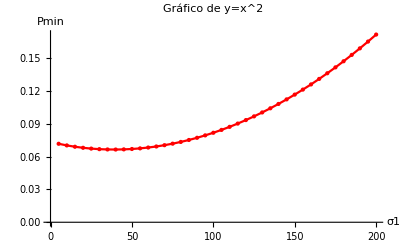

```mathematica
ListPlot[Fig3D2,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\DenseGaussian100H.mat",Fig3D2];
```

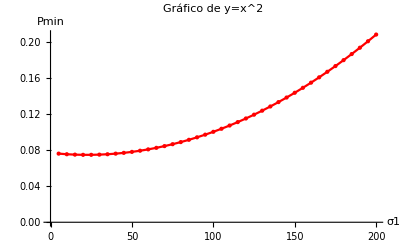

```mathematica
ListPlot[Fig3D2,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\DenseGaussian50H.mat",Fig3D2];
```

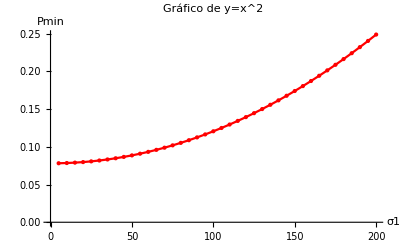

```mathematica
ListPlot[Fig3D2,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\DenseGaussian0H.mat",Fig3D2]
```

C:\Users\adm-wolfram\Documents\Resultados\Paper-Revista\DenseGaussian0H.mat

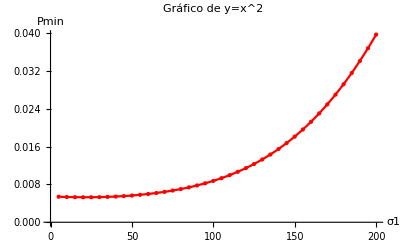

```mathematica
ListPlot[Fig3D2,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\SubUrbanGaussian150.mat",Fig3D2]
```

C:\Users\adm-wolfram\Documents\Resultados\Paper-Revista\SubUrbanGaussian150.mat

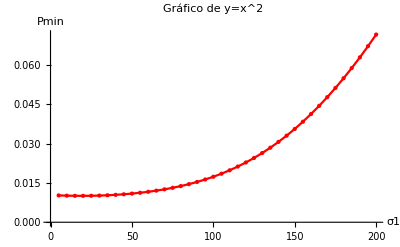

```mathematica
ListPlot[Fig3D2,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\SubUrbanGaussian100.mat",Fig3D2]
```

C:\Users\adm-wolfram\Documents\Resultados\Paper-Revista\SubUrbanGaussian100.mat

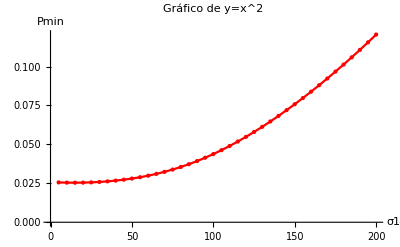

```mathematica
ListPlot[Fig3D2,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\SubUrbanGaussian50.mat",Fig3D2]
```

C:\Users\adm-wolfram\Documents\Resultados\Paper-Revista\SubUrbanGaussian50.mat

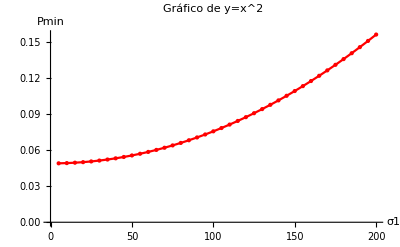

```mathematica
ListPlot[Fig3D2,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\SubUrbanGaussian0.mat",Fig3D2]
```

C:\Users\adm-wolfram\Documents\Resultados\Paper-Revista\SubUrbanGaussian0.mat